## Section 1: A basic application for a single building

## Overview

In this section we will build a simple application that will allow students to track all of the energy consumption of a single building.  The first chapter provides the very basic building blocks required to build an application to record, save and plot daily kwh register readings from a single electric meter.  In the second chapter we will add the ability to manage additional commodities, as well as different data types, such as interval data.  We will also learn how to import data from a spreadsheet.  In the third chapter we tie the individual components from the first two chapters into an application that can track all of the energy consumed by a single building.

## Chapter 1: Recording Register Readings from an Electric Meter

## Background

In this chapter we will learn how to record, save and plot daily kwh register readings from a single electric meter.  We will learn the basics of plotting TimeSeries, and we will learn how to store information in a CloudExpression.  The use of a CloudExpression allows us to create a browser accessible form to add new data, and create browser accessible visualizations so that information collected by the group can be shared.

### Register Readings

If students will be recording energy consumption directly from the face of the meter they will be recording register readings.

The values displayed on a typical electric or gas meter represent the total quantity of the commodity measured by the meter since it was installed.  The values start at zero when the meter is installed, and increment with each unit of the commodity measured.  In early meters the quantity measured was represented by dials that rotated as the commodity flowed through the meter.  In modern meters the quantity measured is typically displayed on an LCD.  With either display type there is a limit to the number of digits that can be displayed.  Once the maximum value is reached for all dials, or digits, the values roll over to zeros, and continue to increase from zero.

```mathematica
WebImageSearch["electric meter","Images",MaxItems->5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Take care to note the unit and direction of the register value you record.  Modern meters are capable of recording measurements for several units of measure in both directions.  There should be a unit of measure indicator as in the image below.  In addition to kilowatt hours you may see maximum kilowatts or kilovar hour units as well.  We will return to these measurements in a later user story.  If your meter is configured to measure energy in both direction you will see two different kilowatt hour register values, one for each direction.  The values may be distinguished by the sign of the values with positive values typically representing energy delivered by the utility to the customer, and negative values representing energy delivered by the customer to the utility.

### Time Series

```mathematica
TextSentences[WikipediaData["time series"]][[;;6]]
```

{A time series is a series of data points indexed (or listed or graphed) in time order.,Most commonly, a time series is a sequence taken at successive equally spaced points in time.,Thus it is a sequence of discrete-time data.,Examples of time series are heights of ocean tides, counts of sunspots, and the daily closing value of the Dow Jones Industrial Average.,Time series are very frequently plotted via line charts.,Time series are used in statistics, signal processing, pattern recognition, econometrics, mathematical finance, weather forecasting, earthquake prediction, electroencephalography, control engineering, astronomy, communications engineering, and largely in any domain of applied science and engineering which involves temporal measurements.}

Time series are core to this application both conceptually and from a code perspective.  The Wolfram Language has a rich set of functionality for performing calculations on and visualising time series. To fully take advantage of that functionality the data must be represented as a TimeSeries object.   As the documentation for the TimeSeries function clarifies the input necessary to create a TimeSeries object is a list of time-value pairs.  For reasons that will become clear when we cover storing data as CloudExpressions, I recommend that data be stored as a list of time-value pairs, instead of as a TimeSeries object.

## User Stories

### Create a list of daily kilowatt hour register readings

#### Story Details

As a participant in my school’s energy tracking initiative I want to create a list of daily kilowatt hour register readings running from 8 days ago to the day before yesterday.

#### Code Explanation

This first operation creates a List of time-value pairs named registerReadings.  Date-time values can be specified in a number of ways within the Wolfram Language but the DateObject provides the most robust means of specifying a date and time.  The value of each time-value pair could be specified as an Integer or Real, however  In this case using the QuantityMagnitude function allows us to assign kilowatt hour units to the value.

Note the date functions used to specify the date in the list below.  Typically you would specify a DateObject with a specific date, such as DateObject[{2019,11,7}].  In this case the relative dates will ensure that as you evaluate the code in this user story, and in subsequent stories within this chapter, you will have a continuous series of dates.  Following this chapter we will almost always use specific dates.

```mathematica
registerReadings={{DatePlus[Yesterday,-7],QuantityMagnitude[Quantity[0, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-6],QuantityMagnitude[Quantity[3, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-5],QuantityMagnitude[Quantity[10, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-4],QuantityMagnitude[Quantity[17, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-3],QuantityMagnitude[Quantity[25, "Hours" "Kilowatts"]]},{DatePlus[Yesterday,-2],QuantityMagnitude[Quantity[35, "Hours" "Kilowatts"]]},
{DatePlus[Yesterday,-1],QuantityMagnitude[Quantity[40, "Hours" "Kilowatts"]]}
}
```

{{Day: Thu 31 Oct 2019,0},{Day: Fri 1 Nov 2019,3},{Day: Sat 2 Nov 2019,10},{Day: Sun 3 Nov 2019,17},{Day: Mon 4 Nov 2019,25},{Day: Tue 5 Nov 2019,35},{Day: Wed 6 Nov 2019,40}}

This next operation creates a TimeSeries object named registerReadingsTimeSeries by using the registerReadings list from the prior operation as the input to the TimeSeries function.  The resulting TimeSeries object can be used in a number of TimeSeries operations from visualizations to calculations.

```mathematica
registerReadingsTimeSeries=TimeSeries[registerReadings]
```

TimeSeries[…]

### Create a plot of daily register readings

#### Story Details

As a participant in my school’s energy tracking initiative, I want to be able to plot a series of the daily register readings that my group has recorded for a single meter.

#### Background

Plotting time series data with time on the x axis and the values on the Y axis provides an intuitive means of exploring data.  While the difference between each register reading is often more interesting, as the difference is the consumption of the commodity between the two register readings, we will start with plotting the register readings themselves.

#### Code Explanation

Plotting TimeSeries data is as simple as applying the DateListPlot to a TimeSeries object.  While this simplest use of DateListPlot is informative, there is a rich set of options that can be used to add annotations, and style to your plots.

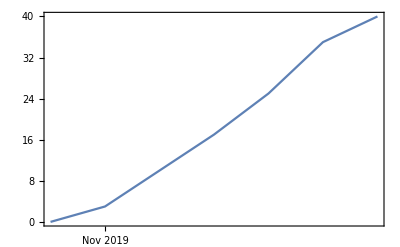

```mathematica
DateListPlot[registerReadingsTimeSeries]
```

A marker can be added for each data point by using PlotMarkers as an option.

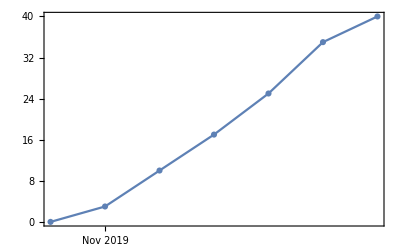

```mathematica
DateListPlot[
registerReadingsTimeSeries,
PlotMarkers->Automatic]
```

Each data point can be labeled with its value.

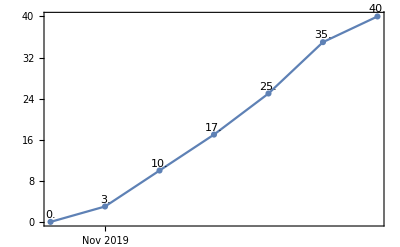

```mathematica
DateListPlot[
registerReadingsTimeSeries,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

A number of  PlotTheme and PlotStyle options can be applied.

```mathematica
DateListPlot[
registerReadingsTimeSeries,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Marketing"]
```

-Graphics-

### Calculate and plot daily consumption using daily register readings

#### Story Details

As a participant in my school’s energy savings initiative,  I want to be able to plot the daily usage captured by  register readings.

#### Code Explanation

For reference we start with one of the plots from the prior user story.

```mathematica
DateListPlot[
registerReadingsTimeSeries,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

-Graphics-

All that is needed to calculate, and plot, the daily consumption captured by the register readings is to apply the Differences function to the registerReadingsTimeSeries.  Differences calculates the difference between successive values in a TimeSeries, or List.

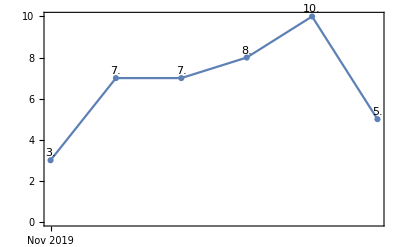

```mathematica
DateListPlot[
Differences[
registerReadingsTimeSeries],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

Another presentation option is a BarChart.

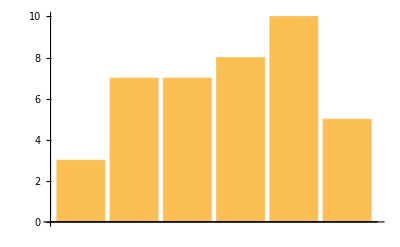

```mathematica
BarChart[Differences[registerReadingsTimeSeries]]
```

### Store Daily Register Reading Values in a CloudExpression

#### Story Details

As a participant in my school’s energy tracking initiatives who has created a list of register readings for an electricity meter I want to store those readings in a way that makes them easily available to other participants, and applications.

#### Background Information

By storing data in a CloudExpression we can make that data available to other participants, or to applications that may make use of the data.  CloudExpressions can be protected with the Wolfram Language’s built in Permissions capability.  They can be made Publicly accessible, they can be made accessible only to those with specific Wolfram IDs, or any user with a specific PermissionsKey.  It is also possible to define different levels of permissions for different groups or applications.

#### Code Explanation

This code takes advantage of the registerReadings list defined in the first user story.  Only the Owner is granted access to the CloudExpression if no other Permissions are set.

```mathematica
registerReadingsCloudExpression=CreateCloudExpression[registerReadings,"registerReadingsCloudExpression"]
```

CloudExpression[…]

This code returns the current permissions of the CloudExpression.

```mathematica
Options[registerReadingsCloudExpression,Permissions]
```

{Permissions→{Owner→{Read,Write,Execute}}}

This code provides public read access, while still providing the owner with complete Read, Write, Execute access.

```mathematica
SetPermissions[registerReadingsCloudExpression,"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

```mathematica
Options[registerReadingsCloudExpression,Permissions]
```

{Permissions→{All→{Read},Owner→{Read,Write,Execute}}}

### Graph daily register reads and daily usage from the contents of a Cloud Expression

#### Story Details

As a participant in my school’s energy tracking initiative I want to be able to plot the daily register readings and daily consumption from register readings stored in a CloudExpression.

#### Code Explanation

Any user with read permission for the CloudExpression can retrieve the contents of the CloudExpression with the Get function.  The code required to manipulate or plot the contents of a CloudExpression is identical to that used for data of the same structure in the local notebook.  Note the two methods of retrieving the CloudExpression used below.  In the first, Get evaluates a CloudExpression using the name specified in the second argument of CreateCloudExpression from the prior user story.  In the second, Get evaluates the name of the CloudExpression variable defined when the CloudExpression was defined.  This second method will only work using the same kernel session during which the CloudExpression was defined.

```mathematica
DateListPlot[TimeSeries[
Get[CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

-Graphics-

```mathematica
DateListPlot[Differences[TimeSeries[
Get[registerReadingsCloudExpression]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

-Graphics-

### Create a Form for Register Reading Entry in Cloud Expression

#### Story Details

As a participant who is responsible for recording daily register readings, I would like to be able to use a form to enter the data, instead of manually typing the data in code.  I would like the form to assume that the date for the register reading is Yesterday.

### Code Explanation

The Wolfram Language provides the ability to create rich forms for data entry with relative ease.The FormPage function allows you to define a form which will invoke a function that operates on the contents entered into the form.  In this case the form asks for a daily register reading as an integer.  The function appends the entered value, along with yesterday’s date as a date-value pair to the list of date-value pairs that is the CloudExpression that contains register readings.

After you evaluate the code below, enter an integer value and press OK.  If you then evaluate the DateListPlot code below you will see the value that you entered appended to the plot.  Please note that since this form assume’s yesterday’s date, that it should only be used once a day for any meter.  In later stories we will explore ways to specify the date.

```mathematica
FormPage[
{"KWH"->"Integer"},
AppendTo[CloudExpression["registerReadingsCloudExpression"],{Yesterday,#KWH}]&,
AppearanceRules-><|"Title"->"Enter Yesterday's kWh Register Reading",
"Description"->"Enter an integer value"|>]
```

To verify that the form did add a new register reading to the CloudExpression, you can check with a DateListPlot.

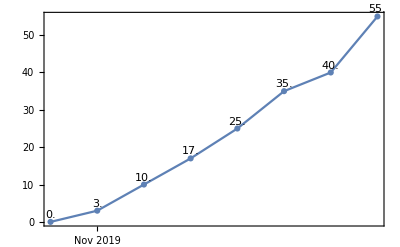

```mathematica
DateListPlot[TimeSeries[Get[
CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic]
```

### Cloud Deploy a Form to Enable Data Entry on a Mobile Device

#### Story Details

As a participant responsible for recording daily register readings I would like to be able to enter the data on a mobile device so that I can record the register reading as I stand at the meter.

#### Code Explanation

A single Wolfram Language function allows you to deploy an enormous array of expressions to the cloud.  In this case, the deployed expression is a form that will append date - value pairs to the CloudExpression that holds your register readings.  As with the CloudExpression that contains the data, you will likely wish to use Permissions to limit access to the forms.  If you use Permissions, participants will need to log in to their Wolfram account to access the forms.  The Cloud Permissions Control Guide provides an overview of the available Permissions functions.

Without adding additional Permissions, only the user with the Wolfram ID that executes the CloudDeploy function will have access to the form.

To access the deployed form, simply open the URL returned by the function.  Note that this form uses Today, where the prior form used Yesterday.

```mathematica
CloudDeploy[FormPage[
{"KWH"->"Integer"},
AppendTo[CloudExpression["registerReadingsCloudExpression"],{Today,#KWH}]&,
AppearanceRules-><|"Title"->"Enter Today's kWh Register Reading",
"Description"->"Enter an integer value"|>]]
```

CloudObject[https://www.wolframcloud.com/obj/291510cb-5798-4263-bf1e-3d2c8ec24eff]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/291510cb-5798-4263-bf1e-3d2c8ec24eff"]⟦1⟧]
```

### Publish A Graph of Register Readings Contained in the Cloud Expression

#### Story Details

As a participant in my school’s energy tracking initiative  I want to be able to view a graph of the register readings recorded by my group on a website, or other similar publication method.

#### Background Information

The Wolfram Language provides a variety of mechanisms for publishing content.  Two of the easiest are to CloudDeploy an expression, or generate EmbedCode that would allow you to embed code within an iFrame.  We will explore other methods of publication in later modules, as well as publish more complex artifacts.

#### Code Explanation

This code adds a PlotLabel, and PlotTheme to the graph, but the code is otherwise identical to the code we have used to plot this data throughout the module.

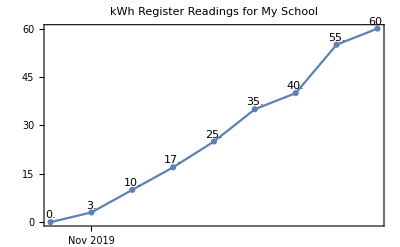

```mathematica
DateListPlot[
TimeSeries[Get[CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotLabel->"kWh Register Readings for My School",
PlotTheme->"Detailed"]
```

To deploy the chart so that it can be viewed through a browser you use the CloudDeploy function with the same code used above.  By including the Delayed function, we ensure that the plot evaluates  when someone accesses the deployed expression.  This ensures that when the expression is accessed following the addition of register readings to the CloudExpression it reflects the current data.  Without inclusion of Delayed the deployed expression will always reflect the state of the data at the time of deployment.

```mathematica
CloudDeploy[Delayed[
DateListPlot[
TimeSeries[Get[CloudExpression["registerReadingsCloudExpression"]]],
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotLabel->"kWh Register Readings for My School",
PlotTheme->"Detailed"]]]
```

CloudObject[https://www.wolframcloud.com/obj/88b71411-5dca-4740-97bc-4cdcc00e7c3d]

```mathematica
SetPermissions[%,"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}